# Лабораторная 13

Выполнила студентка ММФ БГУ 
КМ, 1 к, 5 гр. Бельская Е.А.
    1 декабря 2019

## Конструкторы точка, вектор, прямая

```mathematica
(*точка*)
ClearAll[kmPoint];
(*конструкторы*)
kmPoint[coord:{_,_}]:=kmPoint[km,"",coord]
kmPoint[id_String,coord:{_,_}]:=kmPoint[km, id,coord]
kmPoint[{ϕ_,r_},"pol"]:=kmPoint[km,"",{r*Cos[ϕ],r*Sin[ϕ]} ]
kmPoint[id_String,{ϕ_,r_},"pol"]:=kmPoint[km,id,{r*Cos[ϕ],r*Sin[ϕ]}]
(*запросы свойств*)
kmPoint[km,id_String,___,coord_List,___]["coord"]:=coord;
kmPoint[km,id_String,___]["id"]:=If[id=="","Точка",id];
kmPoint[km,id_String,___,coord_List,___]["coord"]:=coord;
kmPoint[km,id_String,___]["id"]:=If[id=="","Точка",id];
NamedQ[kmPoint[km,id_String,__]]^:=id≠""

(*вектор*)
ClearAll[kmVector];
(*конструкторы*)
kmVector[id_String, coord:{_,_}]:=kmVector[km,id,coord]
kmVector[ coord:{_,_}]:=kmVector[km,"",coord]
kmVector[id_String, P0_kmPoint, P1_kmPoint]:=kmVector[id,P0@"coord"-P1@"coord"]
kmVector[ P0_kmPoint, P1_kmPoint]:=kmVector[If[And@@NamedQ/@{P0,P1},StringJoin[P0@"id",P1@"id"]," "],P0@"coord"-P1@"coord"]
kmVector[id_String,v_kmVector,d_]:=kmVector[id,v@"coord"*d]
kmVector[v_kmVector,d_]:=kmVector[If[And@@NamedQ/@{P0,P1},StringJoin[P0@"id",P1@"id"]," "],v@"coord"*d]
(*запросы свойств*)
kmVector[km,id_String,__]["id"]:=If[id=="","Vector",id]
kmVector[km,__,coord:{_,_}]["coord"]:=coord;
kmVector[km,__,coord:{_,_}]["length"]:=√(coord.coord);
kmVector[km,__,coord:{_,_}]["ort"]:=kmVector[coord/(√(coord.coord))]
NamedQ[kmVector[km,id_String,__]]^:=id≠""
NamedQ[kmLine[km,id_String,__]]^:=id≠""
(*прямая*)
ClearAll[kmLine];
(*конструкторы*)
kmLine[id_String, A_.x_+B_.y_+C_.==0,{x_Symbol,y_Symbol}]:=kmLine[km,id,{A,B,C}]/;¬PossibleZeroQ[Abs@A+Abs@B];
kmLine[id_String,A_.x_+C_.==0,{x_Symbol, _Symbol}]:=kmLine[km,id,{A,0,C}];
kmLine[id_String,B_.y_+C_.==0,{_Symbol, y_Symbol}]:=kmLine[km,id,{0,B,C}];
kmLine[km,"",{A_,B_,_}]:=Abort[]/;PossibleZeroQ[Abs@A+Abs@B]
kmLine[equ:(__==0),vars:{_Symbol,_Symbol}]:=kmLine["",equ,vars]
kmLine[id_String,P0_kmPoint,Dir_kmVector]:=kmLine[id,Det[{Dir@"coord",{x,y}-P0@"coord"}]==0,{x,y}]
(*kmLine[id_String,P0_kmPoint,Dir_kmVector]:=kmLine[km,id,Append[#,-#.P0["coord"]]&[({{0, -1}, {1, 0}}).Dir@"coord"]]*)
kmLine[P_kmPoint,Dir_kmVector]:=kmLine[If[And@@(NamedQ/@{P,Dir}),StringJoin[P@"id",Dir@"id"],""],P,Dir]
kmLine[id_String,P0_kmPoint,P1_kmPoint]:=kmLine[id,P0,kmVector[P1,P0]]
kmLine[P0_kmPoint,P1_kmPoint]:=kmLine[If[And@@(NamedQ/@{P0,P1}),StringJoin[P0@"id",P1@"id"],""],P0,P1]
kmLine[id_String,P0_kmPoint,N_kmVector,"⊥"]:=kmLine[id,P0,kmVector[({{0, 1}, {-1, 0}}).N@"coord"]]
kmLine[P0_kmPoint,N_kmVector]:=kmLine[If[And@@(NamedQ/@{P0,N}),StringJoin[P0@"id",N@"id"],""],P0,N]
(*запросы свойств*)
kmLine[km,id_String,__]["id"]:=If[id=="","Прямая",id];
kmLine[km,__, {A_.,B_.,C_.}]["coef"]:={A,B,C};
kmLine[km,__, {A_.,C_.}]["coef"]:={A,C}
kmLine[km,__, {B_.,C_.}]["coef"]:={B,C}
kmLine[km, id_String, coef:{A_.,B_.,C_.}]["equ"]:=(A x+B y + C ==0)
kmLine[km,__, coef:{A_.,B_.,C_.} ]["norm"]:=kmVector[{A,B}]
kmLine[km,___, coef:{A_.,B_.,C_.} ]["dir"]:=kmVector[{-B,A}]
kmVector["⊥",vec_kmVector]:=kmVector[{({{0, -1}, {1, 0}}).vec@"coord"}]
kmLine[P_kmPoint, L_kmLine]:=kmLine[P,L["norm"]]

ClearAll[kmGetTwoLinePoints];
kmGetTwoLinePoints[Line_kmLine]:=Map[kmPoint,If[Apply[Less, Abs@Line["coef"]⟦{1,2}⟧],Table[{x, y}/.First@Solve[Line@"coef".{x, y,1}==0],{x,{-1,1}}],Table[{x, y}/.First@Solve[Line["coef"].{x, y,1}==0],{y,{-1,1}}]]]
```

```mathematica
ClearAll[ kmGraphics2D];
```

```mathematica
kmGraphics2D[ point_List,opts___]:=Graphics[ ReplaceAll[ point,{P_kmPoint :>Tooltip[ Point@P@"coord",Style[Format[Row@{P["id"],"(",Row[P["coord"],","],")"},StandardForm],Large]],L_kmLine:> Tooltip[InfiniteLine@Through@kmGetTwoLinePoints[L]@"coord",Style[ Format[Row@{L["id"],":",L["equ"]} ,StandardForm],Large]]}],opts]
```

## Задание 1.7

```mathematica
kmLine[P_kmPoint,L_kmLine]:=kmLine[P,L["norm"]]
```

```mathematica
BackgroundGrid[PlotRan_,{sL_,sW_},{bL_,bW_},{{xColour_,yColour_},{xTColour_,yTColour_}},opts_]:=Graphics[{},Frame-> True,
PlotRange -> PlotRan,
GridLines -> {
Table[If[Divisible[i,bL],{i,{xTColour,AbsoluteThickness[2]}},{i,xColour}],{i,PlotRan⟦1⟧⟦1⟧,PlotRan⟦1⟧⟦2⟧,sL}],
Table[If[Divisible[i,bW],{i,{yTColour,AbsoluteThickness[2]}},{i,yColour}],{i,PlotRan⟦2⟧⟦1⟧,PlotRan⟦2⟧⟦2⟧,sW}]
},
GridLinesStyle->opts]
```

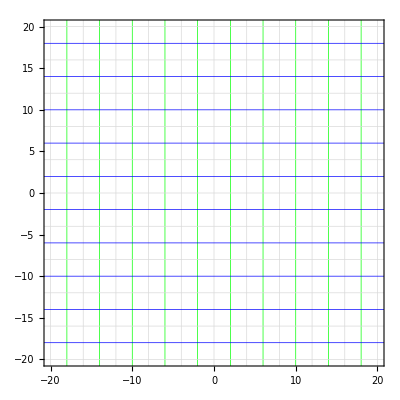

```mathematica
BackgroundGrid[{{-20,20},{-20,20}},{2,2},{4,4},{{Green,Blue},{Gray,Gray}},Directive[Thin]]
```

```mathematica
grids[min_,max_]:=Table[If[Mod[i,5]==0,{i,Black},{i,LightGray}],{i,Ceiling[min],Floor[max],1}]
```

```mathematica
BackgroudGrid1[Size:{x_,y_},m_]:=Graphics[PlotRange->{{-x,x},{-y,y}},Frame->True,GridLines->grids]
```

```mathematica
BackgroudGrid1[{-10,10},Black]
```

```mathematica
BackgroudGrid1[{-10,10},GrayLevel[0]]
```

-Graphics-

## Задание 1.8

```mathematica
ml=kmLine["b",2.5x+y-6==0,{x,y}]
```

kmLine[km,b,{2.5,1,-6}]

```mathematica
mp=kmPoint["a",{5,-3}]
```

kmPoint[km,a,{5,-3}]

```mathematica
nl=kmLine[mp,ml]
```

kmLine[km,,{-1.,2.5,12.5}]

```mathematica
Deploy[DynamicModule[{p=mp["coord"]},kmGraphics2D[{PointSize[0.02],Red,Dynamic@Point[p],Blue,Dynamic@kmLine[kmPoint@p,ml],Locator[Dynamic[p],None],Green,ml},PlotRange->10,Axes-> True]]]
```

## Задание 1.9

```mathematica
kmLine[km, id_String, coef:{A_.,B_.,C_.}]["eq"]:=(A x+B y + C )
```

```mathematica
findpos[P_kmPoint,L_kmLine,vars:{x_,y_}]:=If[(L["eq"]/.x:>P["coord"]⟦1⟧//(#/.y:>P["coord"]⟦2⟧)&)>0, 0,If[(L["eq"]/.x:>P["coord"]⟦1⟧//(#/.y:>P["coord"]⟦2⟧)&)<0, 2,1]]
```

```mathematica
li=kmLine[kmPoint[{0,4}],kmVector[{4,0}]]
```

kmLine[km,,{0,4,-16}]

```mathematica
po=kmPoint[{0,5}]
```

kmPoint[km,,{0,5}]

```mathematica
findpos[po,li,{x,y}]
```

0

## Задание 1.10

```mathematica
Deploy[DynamicModule[{p=po["coord"]},kmGraphics2D[{PointSize[0.02],Locator[Dynamic[p],None],Which[findpos[kmPoint[p],li,{x,y}]==0,Red,findpos[kmPoint[p],li,{x,y}]==2,Green],Dynamic@Point[p],Green,li},PlotRange->10,Axes-> True]]]
```

```mathematica
Manipulate[
Graphics[{
PointSize[0.05],Which[findpos[kmPoint[p],li,{x,y}]==0,Green,findpos[kmPoint[p],li,{x,y}]==2,Blue],Point[p],
Thick,Red,InfiniteLine@Through@kmGetTwoLinePoints[li]@"coord"
},Axes-> True,PlotRange-> 15],
{{p,po["coord"]},Locator}]
```

## Задание 1.11-1.12

```mathematica
kmGetPoint[L_kmLine,L1_kmLine]:=kmPoint[Join[x/.Solve[(y/.First@Solve[L@"coef".{x, y,1}==0])-(y/.First@Solve[L1@"coef".{x, y,1}==0])==0,x],y/.Solve[(x/.First@Solve[L@"coef".{x, y,1}==0])-(x/.First@Solve[L1@"coef".{x, y,1}==0])==0,y]]]
```

```mathematica
kmGetPoint[l1,l2]
```

kmGetPoint[l1,l2]

```mathematica
p1=kmPoint[{-5,5}];
p2=kmPoint[{5,-5}];
p3=kmPoint[{-5,-5}];
p4=kmPoint[{5,5}];
l1=kmLine[p1,p2];
l2=kmLine[p3,p4];
```

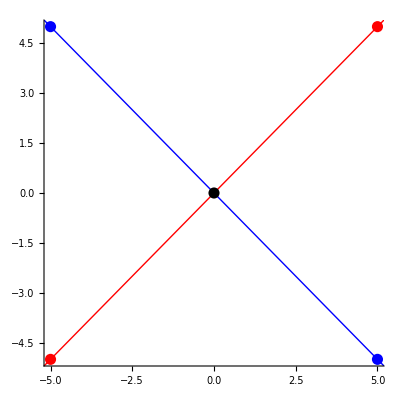

```mathematica
kmGraphics2D[{Blue,PointSize[0.02],p1,p2,kmLine[p1,p2],Red,p3,p4,kmLine[p3,p4],Black,kmGetPoint[kmLine[p1,p2],kmLine[p3,p4]]},Axes-> True]
```

```mathematica
DynamicModule[{p1=p1["coord"],p2=p2["coord"],p3=p3["coord"],p4=p4["coord"]},Dynamic@kmGraphics2D[{PointSize[0.02],Point[#]&/@{p1,p2,p3,p4,kmGetPoint[kmLine[kmPoint@p1,kmPoint@p2],kmLine[kmPoint@p3,kmPoint@p4]]@"coord"},Blue,kmLine[kmPoint@p1,kmPoint@p2],Red,kmLine[kmPoint@p3,kmPoint@p4],Locator[Dynamic[p1],None],Locator[Dynamic[p2],None],Locator[Dynamic[p3],None],Locator[Dynamic[p4],None],Text[Style[Row@{"Toчка пересечения прямых:",kmLine[kmPoint@p1,kmPoint@p2]@"equ",";   "},Black,Thick],{0,20}],Text[Style[kmLine[kmPoint@p3,kmPoint@p4]@"equ",Black,Thick],{0,18}]},Axes-> True,PlotRange->20]]
```

## Задание 1.14 - 1.15

```mathematica
{a,b,c,d,e}=kmPoint/@{{1,1},{4,0}, {5,2}, {4,5}, {1, 3}}
```

{kmPoint[km,,{1,1}],kmPoint[km,,{4,0}],kmPoint[km,,{5,2}],kmPoint[km,,{4,5}],kmPoint[km,,{1,3}]}

```mathematica
check[poly_,P_]:=RegionMember[Polygon[poly],P]
```

```mathematica
DynamicModule[{a=a["coord"],b=b["coord"],c=c["coord"],d=d["coord"],e=e["coord"],p={3,3}},Dynamic@kmGraphics2D[{PointSize[0.02],Point[#]&/@{a,b,c,d,e},Point[p,If[check[{a,b,c,d,e},p],VertexColors-> Red,VertexColors-> Blue]],Black,Line[{a,b,c,d,e,a}],Locator[Dynamic[a],None],Locator[Dynamic[p],None],Locator[Dynamic[b],None],Locator[Dynamic[c],None],Locator[Dynamic[d],None],Locator[Dynamic[e],None]},PlotLabel->Style[Column@{If[check[{a,b,c,d,e},p],"Внутри","Снаружи"],kmLine[kmPoint@a,kmPoint@b]@"equ",kmLine[kmPoint@b,kmPoint@c]@"equ",kmLine[kmPoint@c,kmPoint@d]@"equ",kmLine[kmPoint@d,kmPoint@e]@"equ",kmLine[kmPoint@e,kmPoint@a]@"equ"},Black,Thick,Italic],Axes-> True,PlotRange->10]]
```